```mathematica
a1 = a/2 {3, √3};
a2 = a/2 {3, -√3};

d3 = a{-1,0};
d1 = a1+d3;
d2 = a2+d3;

d = {d1, d2, d3};

K = {(2π)/(3a), (2 π)/(3 √3 a)};
K' = {(2π)/(3a), -(2 π)/(3 √3 a)};

k = {kx,ky};

w =Sum[ⅇ^(-ⅈ k.d[[i]]), {i, 1,3}];

Simplify[w /. {kx->K[[1]], ky->K[[2]]}]
```

0

```mathematica
2
```

```mathematica
H = -ⅈ Sum[d[[i]] ⅇ^(-ⅈ K.d[[i]]), {i,1,3}];
H' = -ⅈ Sum[d[[i]] ⅇ^(-ⅈ K'.d[[i]]), {i,1,3}];
q = {qx,qy};

Simplify[q.H ⅇ^((ⅈ  π)/3) ]
Simplify[q.H'  ⅇ^((-ⅈ  π)/3)]
```

-3/2 ⅈ a (qx-ⅈ qy)

-3/4 (-ⅈ+√3) a (qx+ⅈ qy)

```mathematica
H
```

{-ⅈ (a/2+1/2 a ⅇ^(-(2 ⅈ π)/3)-a ⅇ^((2 ⅈ π)/3)),-ⅈ (-(√3 a)/2+1/2 √3 a ⅇ^(-(2 ⅈ π)/3))}

```mathematica
ComplexExpand[ - Exp[(-I Pi)/3 ]]
```

-1/2+(ⅈ √3)/2

```mathematica
ComplexExpand[Exp[(I  2 Pi)/3 ]]
```

-1/2+(ⅈ √3)/2

## Fermiones de Dirac

```mathematica
ww = Grad[w, {kx,ky}] /. {kx->K[[1]], ky->K[[2]]}
```

{-(ⅈ a)/2-1/2 ⅈ a ⅇ^(-(2 ⅈ π)/3)+ⅈ a ⅇ^((2 ⅈ π)/3),1/2 ⅈ √3 a-1/2 ⅈ √3 a ⅇ^(-(2 ⅈ π)/3)}

```mathematica
Simplify[ComplexExpand[q.ww ⅈ ⅇ^((ⅈ π)/3)]]
```

3/2 a (qx-ⅈ qy)

```mathematica
ComplexExpand[ Exp[(- I  Pi)/3 ]]
ComplexExpand[ -  Exp[(I  2 Pi)/3 ]]
```

1/2-(ⅈ √3)/2

1/2-(ⅈ √3)/2

```mathematica
Simplify[- q.ww Exp[-I 2 Pi/3] ]
```

-3/2 ⅈ a (qx-ⅈ qy)

```mathematica
Simplify[ComplexExpand[- Exp[I 2 Pi /3] (I qx-qy)]]
```

1/2 (ⅈ+√3) (qx+ⅈ qy)

```mathematica
Exp[- I Pi/3] == - Exp[I Pi 2 /3]
```

True

```mathematica
Simplify[Simplify[q.ww]-Simplify[- ⅈ (ⅇ^((-ⅈ π)/3) 3a)/2 (qx-ⅈ qy)]]
```

0

```mathematica
M = - ⅈ (ⅇ^((-ⅈ π)/3) 3a)/2 (qx-ⅈ qy)
```

-3/2 ⅈ a ⅇ^(-(ⅈ π)/3) (qx-ⅈ qy)

```mathematica
MM= (-3  a)/2 ⅇ^((-ⅈ 2 π)/3) (ⅈ qx - qy)
```

-3/2 a ⅇ^(-(2 ⅈ π)/3) (ⅈ qx-qy)

```mathematica
Rew = Simplify[ComplexExpand[Re[w]]]

Imw = Simplify[ComplexExpand[Im[w]]]

g[kx_, ky_] :=Imw/Rew
```

Cos[(a kx)/2]^2+2 Cos[(a kx)/2] Cos[1/2 √3 a ky]-Sin[(a kx)/2]^2

2 (Cos[(a kx)/2]-Cos[1/2 √3 a ky]) Sin[(a kx)/2]

```mathematica
g[1,0]
```

(2 (Cos[(a kx)/2]-Cos[1/2 √3 a ky]) Sin[(a kx)/2])/(Cos[(a kx)/2]^2+2 Cos[(a kx)/2] Cos[1/2 √3 a ky]-Sin[(a kx)/2]^2)

```mathematica
P[kx_, ky_] := ArcTan[(2 (Cos[(a kx)/2]-Cos[1/2 √3 a ky]) Sin[(a kx)/2])/(Cos[(a kx)/2]^2+2 Cos[(a kx)/2] Cos[1/2 √3 a ky]-Sin[(a kx)/2]^2)]
```

```mathematica
AbsArg[ComplexExpand[w]]
```

{Abs[Cos[a kx]+Cos[(a kx)/2-1/2 √3 a ky]+Cos[(a kx)/2+1/2 √3 a ky]+ⅈ (Sin[a kx]-Sin[(a kx)/2-1/2 √3 a ky]-Sin[(a kx)/2+1/2 √3 a ky])],Arg[Cos[a kx]+Cos[(a kx)/2-1/2 √3 a ky]+Cos[(a kx)/2+1/2 √3 a ky]+ⅈ (Sin[a kx]-Sin[(a kx)/2-1/2 √3 a ky]-Sin[(a kx)/2+1/2 √3 a ky])]}

```mathematica
g[kx_, ky_]:={Abs[Cos[a kx]+Cos[(a kx)/2-1/2 √3 a ky]+Cos[(a kx)/2+1/2 √3 a ky]+ⅈ (Sin[a kx]-Sin[(a kx)/2-1/2 √3 a ky]-Sin[(a kx)/2+1/2 √3 a ky])],Arg[Cos[a kx]+Cos[(a kx)/2-1/2 √3 a ky]+Cos[(a kx)/2+1/2 √3 a ky]+ⅈ (Sin[a kx]-Sin[(a kx)/2-1/2 √3 a ky]-Sin[(a kx)/2+1/2 √3 a ky])]};
G[kx_, ky_] := g[kx, ky][[1]] {Cos[g[kx, ky][[2]]], Sin[g[kx,ky][[2]]]}
```

```mathematica
G[K[[1]],K[[1]]]
```

{-√((((√3)/2-Cos[π/6-π/(√3)]-Cos[π/6+π/(√3)])^2+(-1/2+Sin[π/6-π/(√3)]+Sin[π/6+π/(√3)])^2)/(1+((√3)/2-Cos[π/6-π/(√3)]-Cos[π/6+π/(√3)])^2/(-1/2+Sin[π/6-π/(√3)]+Sin[π/6+π/(√3)])^2)),-(((√3)/2-Cos[π/6-π/(√3)]-Cos[π/6+π/(√3)]) √((((√3)/2-Cos[π/6-π/(√3)]-Cos[π/6+π/(√3)])^2+(-1/2+Sin[π/6-π/(√3)]+Sin[π/6+π/(√3)])^2)/(1+((√3)/2-Cos[π/6-π/(√3)]-Cos[π/6+π/(√3)])^2/(-1/2+Sin[π/6-π/(√3)]+Sin[π/6+π/(√3)])^2)))/(-1/2+Sin[π/6-π/(√3)]+Sin[π/6+π/(√3)])}

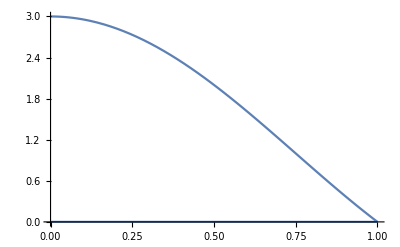

```mathematica
M = {K[[1]],0};

FK[t_] = {t K[[1]], t K[[2]]};
(*KM[t_] = {t (M-K)[[1]] + K[[1]],t (M - K)[[2]] + K[[2]]} ;*)



Through[{FK}@t];
funcs= G@@@% ;

Show[Plot[{funcs},{t,0,1}]]
```

```mathematica
Plot3D[G[kx,ky][[2]], {kx,-4,4}, {ky, -4,4}]
```

-Graphics3D-